# Ecuaciones de estado

```mathematica
(*Importamos archivos de EoS*)
ClearAll["Global`*"];
SoftRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,1]]; SoftP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,2]];
Soft = Transpose[{Flatten[SoftP], Flatten[SoftRho]}];
MidRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,1]]; MidP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,2]];
Mid = Transpose[{Flatten[MidP], Flatten[MidRho]}];
StiffRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,1]]; StiffP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,2]];
Stiff = Transpose[{Flatten[StiffP], Flatten[StiffRho]}];
```

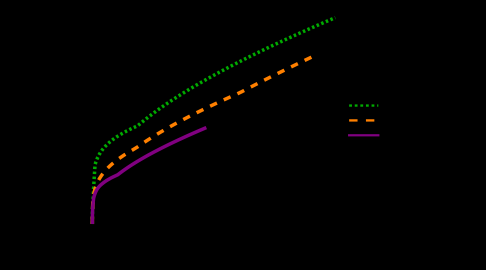

```mathematica
(*Definimos las ecuaciones de estado*)
ρSoft=Quiet[Interpolation[Soft,InterpolationOrder->1]];
ρMid=Quiet[Interpolation[Mid,InterpolationOrder->1]];
ρStiff=Quiet[Interpolation[Stiff,InterpolationOrder->1]];

(* Creamos los plots de cada una *)
SoftPlot=Plot[ρSoft[P],{P,Min[SoftP],Max[SoftP]},PlotStyle->{Darker[Green],Thickness[0.007],Dashing[0.005]}];

MidPlot=Plot[ρMid[P],{P,Min[MidP],Max[MidP]},PlotStyle->{Orange,Thickness[0.007],Dashing[0.015]}];

StiffPlot=Plot[ρStiff[P],{P,Min[StiffP],Max[StiffP]},PlotStyle->{Purple,Thickness[0.007]}];

(* Mostramos los plots con su leyenda *)
Legended[Show[SoftPlot,MidPlot,StiffPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[FontSize->10,Black],FrameLabel->{"P / km^-2","ρ / km^-2"},AspectRatio->3/4,ImageSize->Medium,Background->Transparent,BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotRange->All],Placed[LineLegend[{{Darker[Green],Thickness[0.007],Dashing[0.005]},{Orange,Thickness[0.007],Dashing[0.015]},Purple},{Style["Soft",10],Style["Middle",10],Style["Stiff",10]},LegendFunction->(Framed[#,FrameStyle->Black,Background->White,FrameMargins->0]&),LegendMarkerSize->{30,2},LabelStyle->(FontFamily->"Helvetica"),Spacings->0.15],{0.17,0.81}]]
```

# Perfiles, coeficientes métricos y escalar de curvatura

Pinit = 7.×10^-4

Radio de la estrella: 11.589173 km

Masa total de la estrella: 2.49914 M_⊙

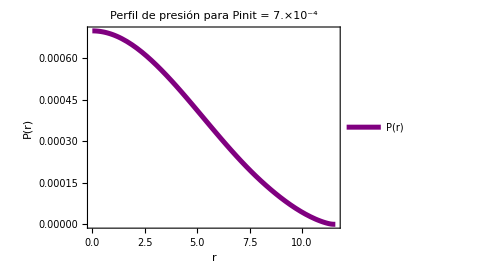
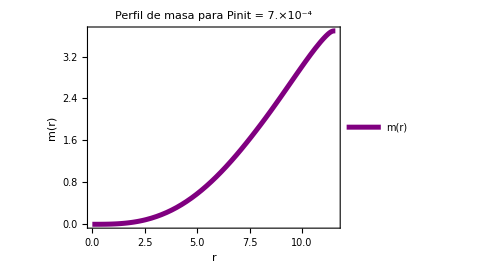
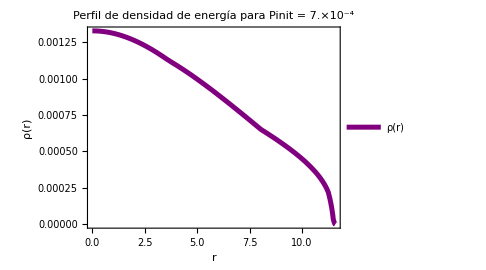

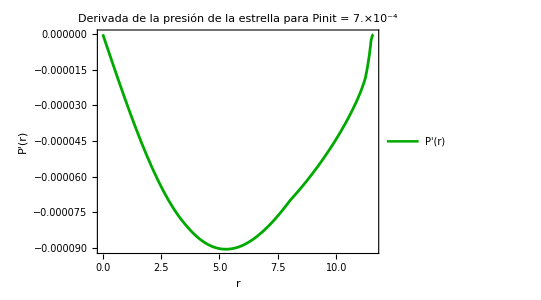

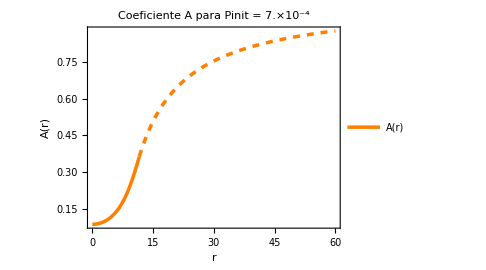
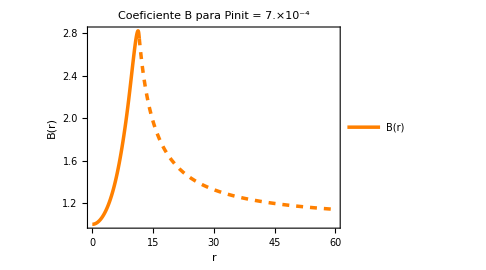

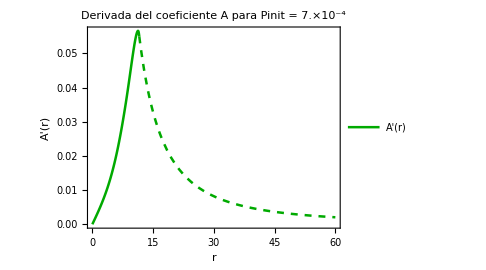
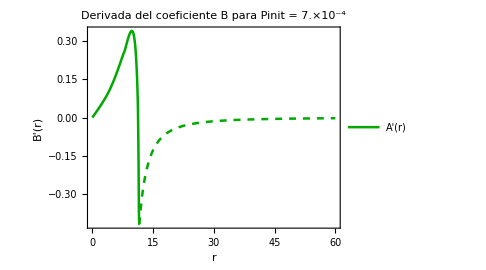

```mathematica
(* Constantes y valores iniciales *)
Msol=1.4763 (*Factor en unidades naturales*);
rinit=1.*10^-10 (*km*);
G=1;
c=1;

(* Aquí decidimos qué EoS usar *)
ρ=ρMid;


(* Fijamos la presión central *)
Pinit=7.*10^-4;

(* Módulo que calcula el cociente entre las soluciones externa e interna del coeficiente A *)
ModuloCociente[Ainit_]:=Module[{de1,de2,de3,de,init,sol,Apeg,cociente,rtot,mtot,Atot},
(*Definición de las ecuaciones*)
de1=P'[r]==-G*ρ[P[r]]*m[r] (1+P[r]/(ρ[P[r]]*c^2)) r^-2 (1+4 Pi*r^3 P[r]/(m[r]*c^2)) (1-2 G*m[r]/(r*c^2))^-1;
de2=m'[r]==4 Pi r^2 ρ[P[r]];
de3=(A'[r])/A[r]==(2*G*(m[r]+4*π*r^3*P[r]))/(r*(r-2*G*m[r]));
de={de1,de2,de3};
init={P[rinit]==Pinit,m[rinit]==10^-50,A[rinit]==Ainit,WhenEvent[P[r]<=7*10^(-10),{rtot=r,mtot=m[r],Atot=A[r],"StopIntegration"}]};
rtot=500;
sol=Quiet[NDSolve[{de,init},{P[r],m[r],A[r]},{r,rinit,500},WorkingPrecision->35],{NDSolve::precw,InterpolatingFunction::dmval}];
Apeg=1-(2*G*mtot)/(c^2*rtot);
cociente=Apeg/Atot;
cociente]

Ainit=0.5*ModuloCociente[0.5];



(* Sistema de ecuaciones en el interior *)
de1=P'[r]==-G*ρ[P[r]]*m[r] (1+P[r]/(ρ[P[r]]*c^2)) r^-2 (1+4 Pi*r^3 P[r]/(m[r]*c^2)) (1-2 G*m[r]/(r*c^2))^-1;
de2=m'[r]==4 Pi r^2 ρ[P[r]];
de3=(A'[r])/A[r]==(2*G*(m[r]+4*π*r^3*P[r]))/(r*(r-2*G*m[r]));
de={de1,de2,de3};
init={P[rinit]==Pinit,m[rinit]==10^-50,A[rinit]==Ainit,WhenEvent[P[r]<=7*10^(-10),{rtot=r,mtot=m[r],Atot=A[r],"StopIntegration"}]};
rtot=500;

(* AQUÍ ESTÁ EL NDSOLVE *)
sol=Quiet[NDSolve[{de,init},{P[r],m[r],A[r]},{r,rinit,500},WorkingPrecision->35],{NDSolve::precw,InterpolatingFunction::dmval}];

(* Extraemos las soluciones *)
pder=sol[[1]][[1]]/. Rule->(#2&);
mder=sol[[1]][[2]]/. Rule->(#2&);
Ader=sol[[1]][[3]]/. Rule->(#2&);
(* Calculamos también B(r) a partir de m(r) *)
Bder=(1-(2*G*mder)/r)^(-1);


(* Calculamos la derivada numérica de P(r) *)
pderivative=D[pder,r];
(* Valores del radio y la masa total de la estrella *)
Print[StringForm["Pinit = ``",DecimalForm[Pinit,ScientificNotationThreshold->{1,1}]]];
Print[StringForm["Radio de la estrella: `` km",NumberForm[rtot,{Infinity,6}]]];
Print[StringForm["Masa total de la estrella: `` ``",NumberForm[mtot/Msol],ToString[Subscript["M","⊙"],StandardForm]]];

(* Representamos P(r) *)
plotP=Plot[pder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","P(r)"},PlotLabel->StringForm["Perfil de presión para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"P(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos m(r) *)
plotm=Plot[mder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","m(r)"},PlotLabel->StringForm["Perfil de masa para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"m(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos ρ(r) *)
ρder=ρ[pder];
plotρ=Plot[ρder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","ρ(r)"},PlotLabel->StringForm["Perfil de densidad de energía para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"ρ(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Hacemos display de estos tres plots *)
Print[plotP,plotm, plotρ];

(* Representamos A(r) *)
plotA= Plot[Ader,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","A(r)"},PlotLabel->StringForm["Coeficiente A para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"A(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos B(r) *)
plotB=Plot[Bder,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","B(r)"},PlotLabel->StringForm["Coeficiente B para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"B(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];

(* Representamos P'(r) *)
Print[Plot[pderivative,{r,rinit,rtot},PlotStyle->{Darker[Green],Thickness[0.005]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","P'(r)"},PlotLabel->StringForm["Derivada de la presión de la estrella para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"P'(r)"},PlotRange->{{0,All},All}]];

(* Calculamos los coefiientes de la métrica en el exterior de la estrella *)
Aext=1-(2*G*mtot)/(c^2*r);
Bext=(Aext)^-1;

(* Representamos los coeficientes para ver el pegado*)
plotAext=Plot[Aext,{r,rtot,60},PlotStyle->{Orange,Thickness[0.007],Dashed},PlotRange->{{0,All},All}];
plotAtot=Show[plotA,plotAext,PlotRange->All];

plotBext=Plot[Bext,{r,rtot,60},PlotStyle->{Orange,Thickness[0.007],Dashed},PlotRange->{{0,All},All}];
plotBtot=Show[plotB,plotBext,PlotRange->All];
Print[plotAtot,plotBtot];

Aderivative=D[Ader,r];
Adderivative=D[Aderivative,r];
AderivativeExt=D[Aext,r];
AdderivativeExt=D[AderivativeExt,r];
Bderivative=D[Bder,r];
Bdderivative=D[Bderivative,r];
BderivativeExt=D[Bext,r];
BdderivativeExt=D[BderivativeExt,r];
plotAderivative=Plot[Aderivative,{r,rinit,rtot},PlotStyle->{Darker[Green],Thickness[0.005]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","A'(r)"},PlotLabel->StringForm["Derivada del coeficiente A para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"A'(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];
plotBderivative=Plot[Bderivative,{r,rinit,rtot},PlotStyle->{Darker[Green],Thickness[0.005]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","B'(r)"},PlotLabel->StringForm["Derivada del coeficiente B para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"A'(r)"},ImageSize->Medium,PlotRange->{{0,All},All}];


plotAderivativeExt=Plot[AderivativeExt,{r,rtot,60},PlotStyle->{Darker[Green],Thickness[0.005],Dashed},PlotRange->{{0,All},All}];
plotAderivativeTot=Show[plotAderivative,plotAderivativeExt,PlotRange->All];
plotBderivativeExt=Plot[BderivativeExt,{r,rtot,60},PlotStyle->{Darker[Green],Thickness[0.005],Dashed},PlotRange->{{0,All},All}];
plotBderivativeTot=Show[plotBderivative,plotBderivativeExt,PlotRange->All];
Print[plotAderivativeTot,plotBderivativeTot];

Rcalc=(Aderivative/(2*Bder*Ader))*(Bderivative/Bder+Aderivative/Ader)-(Adderivative/(Bder*Ader))-(2*Aderivative/(r*Bder*Ader))+(2*Bderivative/(r*Bder^2))-(2/(Bder*r^2))+(2/r^2);
RcalcExt=(AderivativeExt/(2*Bext*Aext))*(BderivativeExt/Bext+AderivativeExt/Aext)-(AdderivativeExt/(Bext*Aext))-(2*AderivativeExt/(r*Bext*Aext))+(2*BderivativeExt/(r*Bext^2))-(2/(Bext*r^2))+(2/r^2);


plotRcalc=Plot[Rcalc,{r,rinit,rtot},PlotStyle->{Blue,Thickness[0.007]},PlotLegends->{"Rcalc(r)"},PlotRange->{{0,All},All}];
plotRcalcExt=Plot[RcalcExt,{r,rtot,80},PlotStyle->{Blue,Thickness[0.007]},PlotRange->{{0,All},All}];
plotRcalctot=Show[plotRcalc,plotRcalcExt,PlotRange->All];

Show[plotRcalctot,PlotLabel->StringForm["Escalar de Ricci comparado para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]]]




Beep[]
```

```mathematica
v
```

```mathematica
(* Exportamos las funciones obtenidas como tablas de puntos *)
npoints=1000;
Int=Table[{r,BdderivativeExt},{r,rtot,60,(60-rtot)/(npoints-1)}];
Export["/Users/neturo/Desktop/BdderivativeExt_7e-4_RG.txt",Int,"Table"];
(*Ext=Table[{r,RcalcExt},{r,rtot,20000,(20000-rtot)/(npoints-1)}];
Export["/Users/neturo/Desktop/RderExt_7e-4_RG.txt.txt",Ext,"Table"];*)
```

# Geodésicas, precesión de la órbita y deflexión de la luz

```mathematica
(*Inversa del radio inicial*)
RadioInicialOrbita=5.*10^2;

Uinit=1/RadioInicialOrbita;

(*Seleccionar materia o luz*)
ϵ=1; (* Null -> 0, Timelike -> 1 *)

If[ϵ==1, 
(*Para partículas masivas,energía ligeramente modificada con respecto a la de la órbita circular*)
k=((1/Uinit)-2*mtot)/Sqrt[(1/Uinit)*((1/Uinit)-3*mtot)];
k=0.999;
(*Para partículas masivas, momento angular de la órbita circular*)
h=(1/Uinit)*Sqrt[(mtot)/((1/Uinit)-3*mtot)];
h=20;
h=Sqrt[Abs[k^2/(1-2*mtot*Uinit)-1]];
ϕmax=30.*Pi;
]

If[ϵ==0,
(*Para partículas sin masa*)
k=1;
h=40;
ϕmax=2Pi;
]


(*.Cambiar las funciones numéricas de r a ϕ*)
AdeϕExt=Aext /. r->1/(U[ϕ]);
BdeϕExt=Bext/. r->1/(U[ϕ]);

(* Iniciales *)
AdeϕExtInit=AdeϕExt/.U[ϕ]->Uinit;
BdeϕExtInit=BdeϕExt/.U[ϕ]->Uinit;

(*Definir la ecuación diferencial*)
eq=2*BdeϕExt*U''[ϕ]==-2*U[ϕ]-(k^2/h^2)*(D[AdeϕExt,U[ϕ]]/AdeϕExt^2)-(D[BdeϕExt,U[ϕ]]/BdeϕExt)*((1/(AdeϕExt*h^2))*(k^2-AdeϕExt*ϵ^2)-U[ϕ]^2);

If[ϵ==0,initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]<=1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Rayo doblado"]}],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Colisión"]}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,8 Pi},WorkingPrecision->35,MaxSteps->1000000];
]

If[ϵ==1,ϕmax=30.0*Pi;
initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",Print["Colisión"]}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,ϕmax},WorkingPrecision->35,MaxSteps->1000000];
]


Udeϕ[ϕ_]:=Evaluate[U[ϕ]/. solGeodU]
rdeϕ[ϕ_]:=1/Udeϕ[ϕ]

(*Graficar la solución*)
If[ϵ==1,
Plot[rdeϕ[ϕ],{ϕ,0,8*Pi},PlotLabel->"r(ϕ)",AxesLabel->{"ϕ","r"}]
]

If[ϵ==0,
Plot[rdeϕ[ϕ],{ϕ,0,ϕmax},PlotLabel->"r(ϕ)",AxesLabel->{"ϕ","r"}]
]

Beep[]
```

NDSolve::precw: The precision of the differential equation ({{2 Bext U''[ϕ]==0.-2 U[ϕ],U[0]==0.002,U'[0]==√Abs[102.858 Plus[«2»] Power[«2»] Power[«2»]-Power[«2»] Power[«2»]]},{},{},{},{WhenEvent[U[ϕ]≥1/rtot,{ϕmax=ϕ,Umax=U[ϕ],StopIntegration,Print[Colisión]}]}}) is less than WorkingPrecision (35.).

NDSolve::ndinnt: Initial condition √Abs[-(4.000000000000000166533453693773483×10^-6)/Bext+(102.8583237795996438990187016315758 (0.9980010000000000269793076768110041-«1»))/(Aext Bext)] is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{2 Bext U''[ϕ]==0.-2 U[ϕ],{U[0]==0.002,U'[0]==√Abs[Plus[«2»]],WhenEvent[U[ϕ]≥1 Power[«2»],{ϕmax=ϕ,Umax=U[«1»],StopIntegration,Print[Colisión]}]}},U[ϕ],{ϕ,0,94.2478},WorkingPrecision→35,MaxSteps→1000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000513426 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{2 Bext U''[0.000513426]==0.-2 U[0.000513426],{U[0]==0.002,U'[0]==√Abs[Plus[«2»]],WhenEvent[U[0.000513426]≥1 Power[«2»],{ϕmax=0.000513426,Umax=U[«1»],StopIntegration,Print[Colisión]}]}},U[0.000513426],{0.000513426,0,94.2478},WorkingPrecision→35,MaxSteps→1000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ioppf: Value of option MaxSteps -> 1.×10^6 should be a positive integer or Infinity.

ReplaceAll::reps: {NDSolve[{2. Bext U''[0.000513426]==0.-2. U[0.000513426],{U[0.]==0.002,U'[0.]==√Abs[Plus[«2»]],WhenEvent[U[0.000513426]≥1. Power[«2»],{ϕmax=0.000513426,Umax=U[«1»],StopIntegration,Print[Colisión]}]}},U[0.000513426],{0.000513426,0.,94.2478},WorkingPrecision→35.,MaxSteps→1.×10^6]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.513427 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{2 Bext U''[0.513427]==0.-2 U[0.513427],{U[0]==0.002,U'[0]==√Abs[Plus[«2»]],WhenEvent[U[0.513427]≥1 Power[«2»],{ϕmax=0.513427,Umax=U[«1»],StopIntegration,Print[Colisión]}]}},U[0.513427],{0.513427,0,94.2478},WorkingPrecision→35,MaxSteps→1000000]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 1.×10^6 should be a positive integer or Infinity.

NDSolve::dsvar: 1.02634 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::ioppf: Value of option MaxSteps -> 1.×10^6 should be a positive integer or Infinity.

General::stop: Further output of NDSolve::ioppf will be suppressed during this calculation.

-Graphics-

## Representación de las órbitas y cálculo de la precesión/deflexión

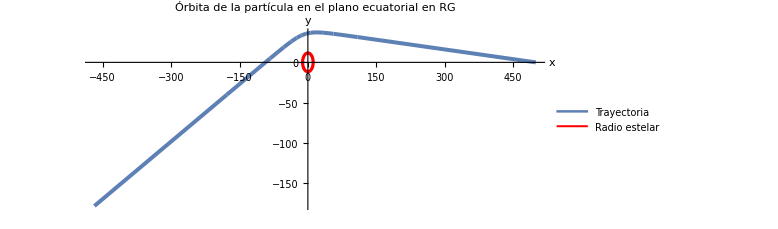

El parámetro de impacto asintótico es b_infty = 39.998111km

El parámetro de impacto tangencial es b_tan = 35.616181km

La deflexión de la luz es de 0.523065 radianes, o 29.969441.ba.

```mathematica
x[ϕ_]:=Cos[ϕ]*rdeϕ[ϕ]
y[ϕ_]:=Sin[ϕ]*rdeϕ[ϕ] 

rtotX=Cos[η]*rtot;
rtotY=Sin[η]*rtot;

trayectoria=ParametricPlot[{x[ϕ][[1]],y[ϕ][[1]]},{ϕ,0,ϕmax},PlotRange->All,PlotStyle->{Thickness[0.005]},ImageSize->Large,AspectRatio->Automatic,AxesLabel->{"x","y"},PlotLegends->{"Trayectoria"},PlotLabel->"Órbita de la partícula en el plano ecuatorial en RG",PlotPoints->100000,MaxRecursion->14];
rtotplot=ParametricPlot[{rtotX,rtotY},{η,0,2*Pi},PlotStyle->{Red,Thickness[0.004]},PlotLegends->{"Radio estelar"}];

Show[trayectoria,rtotplot,AxesOrigin->{0,0}]



(*Calcular la precesión de la órbita*)
If[ϵ==1,
orbita=Table[{ϕ,rdeϕ[ϕ][[1]]},{ϕ,0,ϕmax,ϕmax/10000}];
apocentros=Most[Rest[FindPeaks[orbita[[All,2]]]]];
angulos=orbita[[All,1]][[apocentros[[All,1]]]];
precesiones=Differences[angulos];
precesionPromedio=Mean[precesiones];
precesionModulo=Mod[precesionPromedio,2 Pi];
Print["La precesión de la órbita es de ",NumberForm[precesionModulo,{Infinity,6}]," radianes, o ", precesionModulo*180/Pi, ".ba"];
soltiempo=NDSolve[{t'[ϕ]==(k/h)*(rdeϕ[ϕ][[1]]^2/(Aext/. r->rdeϕ[ϕ][[1]])),t[0]==0},t[ϕ],{ϕ,0,ϕmax},WorkingPrecision->35,MaxSteps->2000000];tdeϕ=soltiempo[[1]][[1]]/. Rule->(#2&);
tiempos=tdeϕ[[0]]/@angulos;periodos=Differences[tiempos];periodoPromedio=Mean[periodos];precesionTemporal=(precesionModulo*180/Pi)/(periodoPromedio*3.336*10^-6);Print["La precesión temporal del perihelio es de ",NumberForm[precesionTemporal,{Infinity,6}]," grados por segundo"];
]

(*Calcular la curvatura de la luz*)
If[ϵ==0,
(*Calcula las derivadas*)
dxdϕ[ϕ_]=D[x[ϕ],ϕ];
dydϕ[ϕ_]=D[y[ϕ],ϕ];
vInicio={dxdϕ[0][[1]],dydϕ[0][[1]]};
vFin={dxdϕ[ϕmax][[1]],dydϕ[ϕmax][[1]]};

(*Calcula el ángulo entre los vectores tangentes*)
productoEscalar=vInicio.vFin;
normaInicio=Norm[vInicio];
normaFin=Norm[vFin];
deflexion=ArcCos[productoEscalar/(normaInicio*normaFin)];
If[ϕmax>2 Pi,deflexion=2 Pi-deflexion];
binfty=Norm[Cross[Append[vInicio,0],{RadioInicialOrbita,0,0}]]/normaInicio;
btan=FindMinValue[{rdeϕ[ϕ][[1]],0<=ϕ<=ϕmax},ϕ];
Print["El parámetro de impacto asintótico es b_infty = ",NumberForm[binfty,{Infinity,6}],"km"];
Print["El parámetro de impacto tangencial es b_tan = ",NumberForm[btan,{Infinity,6}],"km"];
Print["La deflexión de la luz es de ",NumberForm[deflexion,{Infinity,6}]," radianes, o ",NumberForm[deflexion*180/Pi,{Infinity,6}],".ba."];
]
```

## Extracción del valor de h para el caso de luz rasante

```mathematica
ModuloRasante[h_]:=Module[{eq,initgeod,solGeodU,Utan,Udeϕ,rdeϕ,colision,return},
colision=True;
(*Definir la ecuación diferencial*)eq=2*BdeϕExt*U''[ϕ]==-2*U[ϕ]-(k^2/h^2)*(D[AdeϕExt,U[ϕ]]/AdeϕExt^2)-(D[BdeϕExt,U[ϕ]]/BdeϕExt)*((1/(AdeϕExt*h^2))*(k^2-AdeϕExt*ϵ^2)-U[ϕ]^2);
initgeod={U[0]==Uinit,U'[0]==Sqrt[Abs[((k^2-AdeϕExtInit*ϵ^2)/(AdeϕExtInit*BdeϕExtInit*h^2))-(U[0]^2/BdeϕExtInit)]],WhenEvent[U[ϕ]<=1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",colision=False}],WhenEvent[U[ϕ]>=1/rtot,{ϕmax=ϕ,Umax=U[ϕ],"StopIntegration",colision=True}]};
(*Resolver numéricamente la ecuación*)
solGeodU=NDSolve[{eq,initgeod},U[ϕ],{ϕ,0,8 Pi},WorkingPrecision->35,MaxSteps->1000000];
If[colision,return=-1,Utan=FindMaxValue[{solGeodU[[1]][[1]][[2]],0<=ϕ<=ϕmax},ϕ];
return=(1/Utan)-rtot];
return]

(*Método de bisección para el valor inicial de A (Ainit).Se hace uso del módulo anterior,y se busca con una tolerancia ϵ*)
δ=10^-5;
maxIter=40;
iter=0;
inf=rtot;
sup=rtot+10;
While[True,iter=iter+1;
med=(inf+sup)/2;
If[iter>maxIter,Print[Style["AVISO: Alcanzado el número máximo de iteraciones",Red]];
Break[]];
If[Abs[ModuloRasante[med]]<δ&&ModuloRasante[med]>0,Break[],If[ModuloRasante[med]*ModuloRasante[inf]<0,sup=med,inf=med]];];

Print["La luz rasante se da con un valor de h = ",med]
```

NDSolve::precw: The precision of the differential equation ({{(2 U''[ϕ])/(1-7.378952076352866715673811583025375 U[«1»])==0.02681298854733293745529769768182695/(1+Times[«2»])^2-2 U[ϕ]-(7.378952076352866715673811583025375 («78» Power[«2»]-Power[«2»]))/(1+Times[«2»]),U[0]==0.002,U'[0]==√Abs[0.00363371-0.985242 Power[«2»]]},«3»,{WhenEvent[U[ϕ]≤1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],StopIntegration,colision$69834=False}],WhenEvent[«1»,«1»]}}) is less than WorkingPrecision (35.).

NDSolve::precw: The precision of the differential equation ({{(2 U''[ϕ])/(1-7.378952076352866715673811583025375 U[«1»])==0.02681298854733293745529769768182695/(1+Times[«2»])^2-2 U[ϕ]-(7.378952076352866715673811583025375 («78» Power[«2»]-Power[«2»]))/(1+Times[«2»]),U[0]==0.002,U'[0]==√Abs[0.00363371-0.985242 Power[«2»]]},«3»,{WhenEvent[U[ϕ]≤1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],StopIntegration,colision$69909=False}],WhenEvent[«1»,«1»]}}) is less than WorkingPrecision (35.).

NDSolve::precw: The precision of the differential equation ({{(2 U''[ϕ])/(1-7.378952076352866715673811583025375 U[«1»])==0.0549401455337703215453401608744932/(1+Times[«2»])^2-2 U[ϕ]-(7.378952076352866715673811583025375 («77» Power[«2»]-Power[«2»]))/(1+Times[«2»]),U[0]==0.002,U'[0]==√Abs[0.00744552-0.985242 Power[«2»]]},{},{},{},{WhenEvent[U[ϕ]≤1/(RadioInicialOrbita+1),{ϕmax=ϕ,Umax=U[ϕ],StopIntegration,colision$69982=False}],«1»}}) is less than WorkingPrecision (35.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

La luz rasante se da con un valor de h = 19.227651177341604408111325326217098

```mathematica
npoints=1000;
Int=Table[{x[ϕ][[1]],y[ϕ][[1]]},{ϕ,0,ϕmax,(ϕmax-0)/(npoints-1)}];
Export["/Users/neturo/Desktop/deflexion_h40_7e-4_RG.txt",Int,"Table"];
```